(For best-quality graphics, evaluate this expression first.)

```mathematica
SetOptions[$FrontEnd,Antialiasing->Automatic,RenderingOptions->{"HardwareAntialiasingQuality"->1}]
```

# How I Made Wine Glasses from Sunflowers

MonthName Day, Year

Christopher Carlson, Technical Communication and Strategy

Eons ago, plants worked out the secret of arranging equal-size seeds in an ever-expanding pattern around a central point so that regardless of the size of the arrangement, the seeds pack evenly.  The sunflower is a well-known example of such a “spiral phyllotaxis” pattern:

-Graphics- |

It’s really magical that this works at all, since the spatial relationship of each seed to its neighbors is unique, changing constantly as the pattern expands outwardly—unlike, say, the cells in a honeycomb, which are all equivalent.  I wondered if the same magic could be applied to surfaces that are not flat, like spheres, toruses, or wine glasses.  It’s an interesting question from an aesthetic point of view, but also a practical one: the answer has applications in space exploration and modern architecture.

To reproduce the flat sunflower pattern mathematically, you need to know three secrets of the arrangement:

1. Seeds spiral outward from the center, each positioned at a fixed angle relative to its predecessor.

2. The fixed angle is the golden angle, γ = 2 π (1-1/Φ), where Φ is the golden ratio.

3. The ith seed in the pattern is placed at a distance from the center proportional to the square root of i.

You can make a picture of that arrangement easily if you think in polar coordinates, with the ith seed placed at coordinate {r, θ}={√i,i γ}:

```mathematica
γ = 2 π (1 - 1/GoldenRatio);
```

```mathematica
PolarCoordinate[r_,θ_]:= r{Cos[θ],Sin[θ]}
```

```mathematica
Graphics[Point[Table[PolarCoordinate[√i,i γ],{i,1,1000}]]]
```

-Graphics-

The reason that the radial distance of the ith seed is proportional to √i is not difficult to understand.  Suppose the ith seed is at distance d from the center. Then the disk of radius d contains i seeds.  In order to achieve an even density of seeds, the number of seeds i in a disk must stand in constant proportion to its area π d^2, or:

i ∝ d^2

Inverting that relationship gives:

d ∝ √i

You can apply the same reasoning to the problem of distributing seeds evenly on a hemisphere. To deal with hemispherical surfaces, it helps to think of the positions of the seeds in fixed-radius spherical coordinates {φ, θ}, where θ plays the same angular role as in polar coordinates and [φ—the angular distance from the north pole along the hemisphere to a point—plays the role of r in polar coordinates.  This figure shows the correspondence between polar coordinates and fixed-radius spherical coordinates:

-Graphics3D--Graphics3D-

The relationship between the area of a spherical cap and its angular radius is not the square root, as in the plane, but something else.  To determine what it is, I started with the expression given in MathWorld for the area of a surface of revolution generated by rotating the parametric curve {x(t), z(t)} about the z-axis:

```mathematica
area = 2 π ∫_Subscript[t, 0]^Subscript[t, 1] x[t] √(x'[t]^2+z'[t]^2)ⅆt
```

For a spherical cap with angular radius ϕ, the generating curve is the circular arc defined by

```mathematica
x[t_] := Sin[t]
z[t_] := Cos[t]
```

as t goes from 0 to φ.

To find the formula for the cap’s area, you don’t need to know anything about integration.  You just plug the values of x, z, t_0=0, and t_1= ϕ into the area formula, and out pops the cap’s area:

```mathematica
2 π ∫_0^φ x[t] √(x'[t]^2+z'[t]^2)ⅆt
```

2 π (1-Cos[φ])

As in the planar case, I wanted i, the number of seeds, to stand in constant proportion to the area of the hemispherical cap, or:

i ∝ (1-Cos[φ])

Introducing c as the constant of proportionality, I found the relationship I sought using Solve:

```mathematica
Solve[i == c(1-Cos[φ]), φ]
```

{{φ→-ArcCos[(c-i)/c]},{φ→ArcCos[(c-i)/c]}}

The two solutions differ in the direction that the seeds spiral around the center.

The constant of proportionality c governs the density of the seeds.  I solved for its value as a function of the total number of seeds n and the maximum angular radius φ_max:

```mathematica
Solve[Subscript[φ, max]== ArcCos[(c-n)/c],c]
```

{{c→-n/(-1+Cos[φ_max])}}

Thus if I want 1,000 seeds in the entire hemisphere, which corresponds to an angular radius φ of 90°, I set c to

```mathematica
-n/(-1+Cos[Subscript[φ, max]]) /. {n->1000, Subscript[φ, max]->90°}
```

1000

Putting all these results together yields the seed-covered hemisphere.  The forms of the coordinate and graphics expressions here are analogous to the forms in the planar case above:

```mathematica
FRSphericalCoordinate[φ_,θ_]:= {Sin[φ] Cos[θ], Sin[φ] Sin[θ], Cos[φ]}
```

```mathematica
Graphics3D[Sphere[
Table[FRSphericalCoordinate[ArcCos[1-(i/1000)],i γ],{i,1,1000}],.04],Boxed->False]
```

-Graphics3D-

If you were building a hemispherical house, this would be the basis of a good roofing pattern, since each equal-sized shingle overlaps the joint between the two below it.  Or, if you wanted to design approximately equal-area flat panels to assemble into a dome, this distribution would be a starting point. This problem of “tectonics”—how to realize curved surfaces with flat materials—is a hot topic in current architectural research.  A similar problem arose in the Starshine 3 student satellite project, which required a spherical sattelite to be evenly covered with reflective mirrors.  The folks at the U.S. Naval Research Laboratory solved that problem with a phyllotaxic pattern.

-Graphics- |

Computing a custom function to cover each new kind of surface was an interesting mathematical journey, but a lot of work.  What I really wanted was a single function that would, once and for all, distribute points evenly on any surface of revolution whose generating curve I could describe parametrically.

As with the disk and hemisphere, the secret to achieving an even distribution of points on an arbitrary surface of revolution is to make the number of points in an area proportional to the area.  Unfortunately, the integral that describes that relationship often has no closed-form solution, even for simple parametric curves.  But fortunately, we don’t need a closed-form solution to obtain a result.  Numerical integration does nicely.

The numerical analog of the area integral above for generating functions x and z, and parameter interval t_0 to t_1, uses the NIntegrate function in place of Integrate:

```mathematica
area[{x_,z_},{t0_,t1_}] :=Abs[NIntegrate[2 π x[t] √((x'[t])^2+(z'[t])^2),{t,t0,t1}]]
```

This function gives area as a function of curve parameter t, but I needed the inverse relationship: given an area, I wanted to know what t is.  Since I couldn’t invert this function directly, I made a table of {area, t} pairs and interpolated that to give myself a function that, from empirical evidence, approximates the inverse sufficiently well:

```mathematica
areaToTFunction[{x_,z_},{t0_,t1_},n_:100]:=
Interpolation[Table[{area[{x,z},{t0,t}],t},{t,t0,t1,N[(t1-t0)/n]}]]
```

With those components, I assembled the function for rendering arbitrary phyllotaxic surfaces. Parameters x and z give the parametric description of the generating curve, {t0,t1} specifies the interval of the curve that generates the surface, density specifies the density of points, and radius gives the radius of the spheres that render the points.

```mathematica
SetAttributes[PhyllotaxicSurface,HoldAll]
```

```mathematica
PhyllotaxicSurface[{x_,z_},{t_,t0_,t1_},density_,radius_]:=
Module[{xFunc,zFunc,tFunc,totalArea,n},
xFunc=Function[t,x];
zFunc=Function[t,z];
tFunc = areaToTFunction[{xFunc,zFunc},{t0,t1}];
totalArea = area[{xFunc,zFunc}, {t0,t1}];
n = Floor[density totalArea];
Graphics3D[{
Sphere[Table[With[{t=tFunc[totalArea i/n],θ=i γ},{xFunc[t] Cos[θ],xFunc[t] Sin[θ],zFunc[t]}],{i,1,n}],radius]
},Boxed->False,ViewAngle->0.3]
];
```

I tested the function with a covering of a complete sphere:

```mathematica
PhyllotaxicSurface[
{Sin[t], Cos[t]}, {t, 0, π}, 200, .05]
```

-Graphics-

As on a sunflower’s disk, the points on the sphere group into spirals that regroup as you move from the poles toward the equator.  To make that structure more apparent, I modified the rendering function so I could specify that every nth point should have a given color, and rendered spheres with n = 2, 3, ..., 13.  The resulting images revealed a variety of spiral structures lurking within the pattern.

```mathematica
spheres = Table[
StripedPhyllotaxicSurface[{Cos[t], Sin[t]}, {t,-π/2, π/2},500,.05,{{White,1},{Black,n}}],{n,2,13}];
```

```mathematica
Grid[Partition[spheres,4],Spacings->{1,1}]
```

-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-

Combinations of colorings layered on top of one another show the complex interplay of spiral structures:

```mathematica
StripedPhyllotaxicSurface[{Cos[t], Sin[t]}, {t,-π/2, π/2},500,.05,{{Yellow,1},{Black,2},{Magenta,3}}]
```

-Graphics-

Since Mathematica’s integration functions are completely general, I could explore generating curves of all sorts, including piecewise and interpolated curves.  Here’s a sample of some phyllotaxic surfaces of revolution I encountered (click an image to see an enlargement):

-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D-

Curious what a phyllotaxic wine glass would look like, I grabbed an image of a Peugeot wine glass from the web and used the Get Coordinates function to digitize its outline, which I fed to Interpolation to get the x and z parametric functions of the curve.  This is the resulting parametric curve:

-Graphics--Graphics-

With those functions, it’s a no-brainer to make a phyllotaxic wine glass.

```mathematica
Show[StripedPhyllotaxicSurface[{wineGlassX[t], wineGlassZ[t]}, {t,1,Length[wineGlassPoints]},.2,2,{{White,1},{Black,2}}],Lighting->"Neutral"]
```

-Graphics3D-

The spiral structures in this form, with its concave and convex surfaces and wide variation of diameters, were especially interesting to explore.  Here’s one study that I particularly liked.  It exploits the fact that when you color every seventh point, you get three distinct spirals at small diameters.  I omitted the other six points entirely so that those spirals stood on their own in the stem, and gave each of them a different color.  By choosing cyan, yellow, and magenta, the base and bowl of the glass are a neutral gray when viewed from a distance, and yet it shimmers almost iridescently as it moves, due to the moiré patterns induced by the patterns on the opposite sides.  The magic of spiral phyllotaxis unites all the parts into one festive whole.

```mathematica
Show[StripedPhyllotaxicSurface[{wineGlassX[t], wineGlassZ[t]}, {t,3,Length[wineGlassPoints]},1,.7,{{Cyan,21,0},{Yellow,21,7},{Magenta,21,14}}],Lighting->"Neutral"]
```

-Graphics3D-

Alas, the effect requires spheres too tiny to bond together, so they’d have to be embedded in a clear glass matrix.  When the day arrives that clear glass can be 3D-printed, I’ll be first in line.  Meanwhile, there are plenty of other intriguing phyllotaxic surfaces waiting to be discovered.

## Implementation

```mathematica
γ = 2 π (1 - 1/GoldenRatio);
```

```mathematica
PolarCoordinate[r_,θ_]:= r{Cos[θ],Sin[θ]}
```

```mathematica
FRSphericalCoordinate[ϕ_,θ_]:= {Sin[ϕ] Cos[θ], Sin[ϕ] Sin[θ], Cos[ϕ]}
```

```mathematica
area[{x_,z_},{t0_,t1_}] :=Abs[NIntegrate[2 π x[t] √((x'[t])^2+(z'[t])^2),{t,t0,t1}]]
```

```mathematica
areaToTFunction[{x_,z_},{t0_,t1_},n_:100]:=
Interpolation[Table[{area[{x,z},{t0,t}],t},{t,t0,t1,N[(t1-t0)/n]}]]
```

```mathematica
SetAttributes[PhyllotaxicSurface,HoldAll]
```

```mathematica
PhyllotaxicSurface[{x_,z_},{t_,t0_,t1_},density_:1,radius_:.5]:=
Module[{xFunc,zFunc,tFunc,totalArea,n},
xFunc=Function[t,x];
zFunc=Function[t,z];
tFunc = areaToTFunction[{xFunc,zFunc},{t0,t1}];
totalArea = area[{xFunc,zFunc}, {t0,t1}];
n = Floor[density totalArea];
Graphics3D[{
Sphere[Table[With[{t=tFunc[totalArea i/n],θ=i γ},{xFunc[t] Cos[θ],xFunc[t] Sin[θ],zFunc[t]}],{i,1,n}],radius]
},Boxed->False,ViewAngle->0.3]
];
```

```mathematica
ClearAll[StripedPhyllotaxicSurface]
```

```mathematica
Atop[a_,b_]:=
MapThread[If[#1===Null,#2,#1]&, {a,b}]
```

```mathematica
Colors[rawColorSpec_,n_]:=
Module[{colorSpec,indices=Range[n], specList},
colorSpec = Take[Append[#,1],3]& /@ rawColorSpec;
specList=With[{c=#[[1]],m=#[[2]],o=#[[3]]},(If[Mod[#-o,m]==0,c,Null]& /@indices)]&/@ colorSpec;
Fold[Atop,Last[specList],Rest[Reverse[specList]]]
];
(*
Colors[{{1,3,2},{2,2,1}},10]
*)
```

```mathematica
ToIndices[colors_]:=
Module[{allColors = Complement[Union[colors],{Null}]},
{#,First /@ Position[colors,#]}& /@ allColors
];
(*
ToIndices[Colors[{{Red,3},{Black,2},{5,5}},10]]
*)
```

```mathematica
SetAttributes[StripedPhyllotaxicSurface,HoldAll]
```

```mathematica
StripedPhyllotaxicSurface[{x_,y_},{t_,t0_,t1_},density_:1,radius_:.5,colorSpec_:{{White,1}}]:=
Module[{xFunc,yFunc,tFunc,totalArea,n},
xFunc=Function[t,x];
yFunc=Function[t,y];
tFunc = areaToTFunction[{xFunc,yFunc},{t0,t1}];
totalArea = area[{xFunc,yFunc}, {t0,t1}];
n = Floor[density totalArea];
Graphics3D[With[{color = #[[1]],indices=#[[2]]},
{color,
Sphere[With[{t=tFunc[totalArea #/n],θ=# γ},{xFunc[t] Cos[θ],xFunc[t] Sin[θ],yFunc[t]}]& /@ indices,radius]}]& /@ ToIndices[Colors[colorSpec,n]],
Boxed->False,ViewAngle->0.3]
];
```

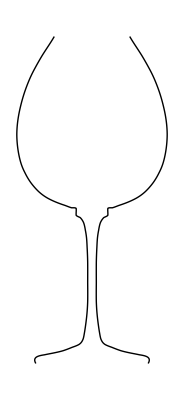

```mathematica
wineGlassPoints = {{172.75,319.75},{177.75,311.75},{183.25,303.25},{189.25,292.75},{193.75,283.75},{198.25,272.25},{201.75,260.25},{204.25,247.75},{205.25,234.75},{204.25,221.75},{201.75,210.25},{198.25,201.75},{193.25,193.25},{186.25,185.25},{178.75,179.75},{170.25,175.75},{163.25,173.25},{157.75,171.25},{153.75,170.75},{153.75,164.75},{150.25,162.75},{147.25,158.25},{145.75,151.75},{144.75,145.25},{144.25,137.25},{143.75,124.25},{143.75,106.25},{143.75,89.75},{144.75,75.75},{146.75,61.75},{148.25,56.25},{151.25,52.75},{157.25,50.25},{165.25,47.25},{173.75,45.25},{181.25,43.75},{188.25,41.75},{188.75,36.25}};
wineGlassX = Interpolation[(First[#]-140)& /@ wineGlassPoints];
wineGlassZ = Interpolation[(Last[#]-36)& /@ wineGlassPoints];
Graphics[{
Line@Table[{wineGlassX[t],wineGlassZ[t]},{t,1,Length[wineGlassPoints],.1}],
Line@Table[{-wineGlassX[t],wineGlassZ[t]},{t,1,Length[wineGlassPoints],.1}]
}]
```